```mathematica
Mean
```

{{1,26},{2,40},{3,59},{4,72},{5,82},{6,88},{7,86},{8,101},{9,94},{10,80},{11,72},{12,47},{13,42},{14,27},{15,17},{16,13},{17,7},{18,3},{19,1},{20,0},{21,1},{22,0},{23,0},{24,0},{25,0}}

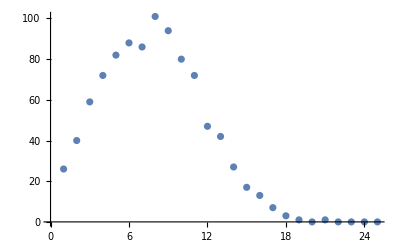

```mathematica
counts=Table[RandomVariate[NormalDistribution[7,4]],{i,1,1000}];
yval=BinCounts[counts,{0,25,1}];
xval=Table[i,{i,1,Length[yval]}];
list=Multicolumn[Join[xval,yval],2]//First
ListPlot[list]
```

{{1,25},{2,35},{3,48},{4,58},{5,88},{6,91},{7,80},{8,92},{9,109},{10,92},{11,64},{12,63},{13,40},{14,24},{15,20},{16,18},{17,5},{18,2},{19,2},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0}}

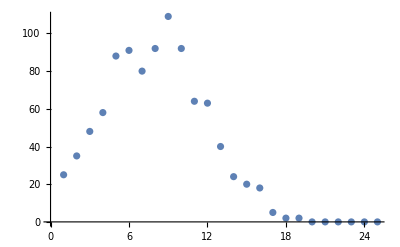

```mathematica
counts=Table[RandomVariate[NormalDistribution[7,4]],{i,1,1000}];
yval=BinCounts[counts,{0,25,1}];
xval=Table[i,{i,1,Length[yval]}];
list=Multicolumn[Join[xval,yval],2]//First
ListPlot[list]
```

{{1,19},{2,38},{3,61},{4,63},{5,85},{6,94},{7,97},{8,103},{9,104},{10,75},{11,61},{12,46},{13,47},{14,20},{15,24},{16,13},{17,5},{18,3},{19,0},{20,1},{21,1},{22,1},{23,0},{24,0},{25,0}}

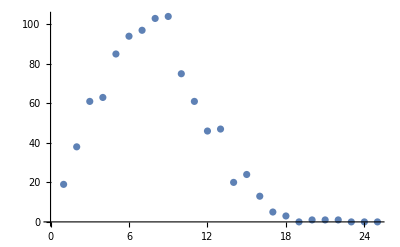

```mathematica
counts=Table[RandomVariate[NormalDistribution[7,4]],{i,1,1000}];
yval=BinCounts[counts,{0,25,1}];
xval=Table[i,{i,1,Length[yval]}];
list=Multicolumn[Join[xval,yval],2]//First
ListPlot[list]
```

{{1,28},{2,41},{3,70},{4,44},{5,84},{6,97},{7,91},{8,101},{9,68},{10,94},{11,77},{12,43},{13,37},{14,33},{15,26},{16,12},{17,5},{18,3},{19,1},{20,0},{21,1},{22,0},{23,0},{24,0},{25,0}}

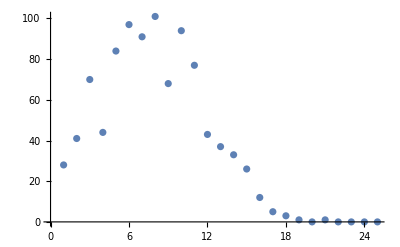

```mathematica
counts=Table[RandomVariate[NormalDistribution[7,4]],{i,1,1000}];
yval=BinCounts[counts,{0,25,1}];
xval=Table[i,{i,1,Length[yval]}];
list=Multicolumn[Join[xval,yval],2]//First
ListPlot[list]
```

{{1,25},{2,31},{3,47},{4,68},{5,89},{6,89},{7,114},{8,108},{9,96},{10,81},{11,80},{12,50},{13,32},{14,18},{15,13},{16,14},{17,3},{18,4},{19,3},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0}}

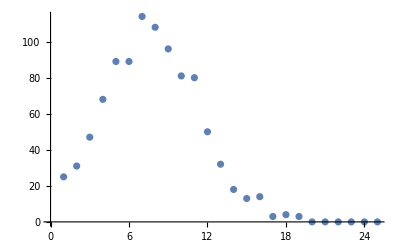

```mathematica
counts=Table[RandomVariate[NormalDistribution[7,4]],{i,1,1000}];
yval=BinCounts[counts,{0,25,1}];
xval=Table[i,{i,1,Length[yval]}];
list=Multicolumn[Join[xval,yval],2]//First
ListPlot[list]
```

```mathematica
Each plot is different because the code generates a new set each time
(following the gaussian distribution). If the seed for the random number
generator was controlled for the plots would look identical.
```